```mathematica
Solve[(ρ2^2*(n-ⅈ)^4-ρ1^2*(n+ⅈ)^4)/(m^2*(n^2+1)^2)==ρ1^2*(n+ⅈ)^2-ρ2^2*(n-ⅈ)^2,n]//Simplify
```

```mathematica
Solve[ρ2^2*(n-ⅈ)^4-ρ1^2*(n+ⅈ)^4==0,n]//FullSimplify
```

{{n→ⅈ+(2 ⅈ √ρ1)/(-√ρ1+√ρ2)},{n→ⅈ-(2 ⅈ √ρ1)/(√ρ1+√ρ2)},{n→-(ⅈ (√ρ1-ⅈ √ρ2)^2)/(ρ1+ρ2)},{n→-(ⅈ (√ρ1+ⅈ √ρ2)^2)/(ρ1+ρ2)}}

```mathematica
Solve[(ρ^2*(n-ⅈ)^4-(n+ⅈ)^4)/(m^2*(n^2+1)^2)==(n+ⅈ)^2-ρ^2*(n-ⅈ)^2,ρ]//FullSimplify
```

{{ρ→-(√(((ⅈ+n)^2+m^2 (1+n^2)^2)/(m^2 (-ⅈ+n)^2)))/(√(((-ⅈ+n)^2+m^2 (1+n^2)^2)/(m^2 (ⅈ+n)^2)))},{ρ→(√(((ⅈ+n)^2+m^2 (1+n^2)^2)/(m^2 (-ⅈ+n)^2)))/(√(((-ⅈ+n)^2+m^2 (1+n^2)^2)/(m^2 (ⅈ+n)^2)))}}

```mathematica
Expand[ρ2^2*(n-ⅈ)^4-ρ1^2*(n+ⅈ)^4]
```

-ρ1^2+4 ⅈ n ρ1^2+6 n^2 ρ1^2-4 ⅈ n^3 ρ1^2-n^4 ρ1^2+ρ2^2+4 ⅈ n ρ2^2-6 n^2 ρ2^2-4 ⅈ n^3 ρ2^2+n^4 ρ2^2

```mathematica
Collect[-ρ1^2+4 ⅈ n ρ1^2+6 n^2 ρ1^2-4 ⅈ n^3 ρ1^2-n^4 ρ1^2+ρ2^2+4 ⅈ n ρ2^2-6 n^2 ρ2^2-4 ⅈ n^3 ρ2^2+n^4 ρ2^2,n]
```

-ρ1^2+ρ2^2+n^2 (6 ρ1^2-6 ρ2^2)+n^3 (-4 ⅈ ρ1^2-4 ⅈ ρ2^2)+n (4 ⅈ ρ1^2+4 ⅈ ρ2^2)+n^4 (-ρ1^2+ρ2^2)

```mathematica
Expand[ρ1^2*(n+ⅈ)^2-ρ2^2*(n-ⅈ)^2]
```

-ρ1^2+2 ⅈ n ρ1^2+n^2 ρ1^2+ρ2^2+2 ⅈ n ρ2^2-n^2 ρ2^2

```mathematica
Collect[-ρ1^2+2 ⅈ n ρ1^2+n^2 ρ1^2+ρ2^2+2 ⅈ n ρ2^2-n^2 ρ2^2,n]
```

-ρ1^2+ρ2^2+n^2 (ρ1^2-ρ2^2)+n (2 ⅈ ρ1^2+2 ⅈ ρ2^2)

```mathematica
(a+bI)^2
```

(a+bI)^2

```mathematica
Expand[(a-b*I)*(a+b*I)]
```

a^2+b^2

```mathematica
Solve[(c-6*n^2*c-2*I*n^3(1+c^2)+2*I*n(1+c^2)+n^4*c)/(m^2*(n^2+1)^2)==c-n^2*c+n*I(1+c^2),c]//FullSimplify
```

{{c→-(ⅈ (1-6 n^2+n^4+m^2 (1+n^2)^2 (-1+n^2+√(1/m^4+(2 (-1+n^2))/m^2+(1+n^2)^2))))/(2 n (2 (-1+n^2)+m^2 (1+n^2)^2))},{c→(ⅈ (-1+6 n^2-n^4+m^2 (1+n^2)^2 (1-n^2+√(1/m^4+(2 (-1+n^2))/m^2+(1+n^2)^2))))/(2 n (2 (-1+n^2)+m^2 (1+n^2)^2))}}

```mathematica
Solve[(c-6*n^2*c-2*I*n^3(1+c^2)+2*I*n(1+c^2)+n^4*c)/(m^2*(n^2+1)^2)==c-n^2*c+n*I(1+c^2),n]//FullSimplify
```

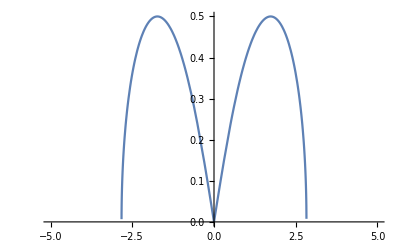

```mathematica
Plot[√(√(x^2+1)-(1+x^2/4)),{x,-5,5}]
```

```mathematica
Solve[√(√(x^2+1)-(1+x^2/4))==0,x]
```

{{x→0},{x→-2 √2},{x→2 √2}}

```mathematica
Manipulate[NSolve[(c-6*n^2*c-2*I*n^3(1+c^2)+2*I*n(1+c^2)+n^4*c)/(m^2*(n^2+1)^2)==c-n^2*c+n*I(1+c^2),n],{c,0,1},{m,0.1,100}]
```

```mathematica
N[√2]
```

1.41421

```mathematica
N[√2,20]
```

1.4142135623730950488

```mathematica
f[c_,m_]:=c-6*n^2*c-2*I*n^3(1+c^2)+2*I*n(1+c^2)+n^4*c-(m^2*(n^2+1)^2)*(c-n^2*c+n*I(1+c^2))
```

```mathematica
f[0,1.42]
```

2 ⅈ n-2 ⅈ n^3-(0.+2.0164 ⅈ) n (1+n^2)^2

```mathematica
NSolve[2 ⅈ n-2 ⅈ n^3-(0.+2.0164 ⅈ) n (1+n^2)^2,n]
```

{{n→0.},{n→0.-0.0521627 ⅈ},{n→0.+0.0521627 ⅈ},{n→0.-1.72891 ⅈ},{n→0.+1.72891 ⅈ}}

```mathematica
Collect[f[0,1.42],n]
```

(0.-0.0164 ⅈ) n-(0.+6.0328 ⅈ) n^3-(0.+2.0164 ⅈ) n^5

```mathematica
Collect[f[0,1.4],n]
```

(0.+0.04 ⅈ) n-(0.+5.92 ⅈ) n^3-(0.+1.96 ⅈ) n^5

```mathematica
g[x_]:= (1.38*10^4)/(x^5+58.76*x^4-1743*x^3+5390*x^2-1.271*10^4*x+9004)
```

```mathematica
g[0.3]
```

2.45136

```mathematica
Collect[Expand[m2^2*ρ2^4*(n-I)^4-m1^2*ρ1^4*(n+I)^4],n]
```

-m1^2 ρ1^4+m2^2 ρ2^4+n^2 (6 m1^2 ρ1^4-6 m2^2 ρ2^4)+n^3 (-4 ⅈ m1^2 ρ1^4-4 ⅈ m2^2 ρ2^4)+n (4 ⅈ m1^2 ρ1^4+4 ⅈ m2^2 ρ2^4)+n^4 (-m1^2 ρ1^4+m2^2 ρ2^4)

```mathematica
Manipulate[NSolve[(c1^6(n/u-I)^4-c2^6(n/u+I)^4)/((n^2/u^2+1)^2)==c2^4(n+I*u)^2-c1^4(n-I*u)^2,n],{c1,0.1,1000},{c2,0.1,1000},{u,0.1,1000}]
```

```mathematica
N[638/232]
```

2.75

```mathematica
N[638/345]
```

1.84928

```mathematica
(2.75+1.84928)/2
```

2.29964

```mathematica
Manipulate[NSolve[(c1^6(n-I*u)^4-c2^6(n+I*u)^4)/((n^2+u^2)^2)==c2^4(n+I*u)^2-c1^4(n-I*u)^2,n],{c1,0.1,1000},{c2,0.1,1000},{u,0.1,1000}]
```

```mathematica
Manipulate[NSolve[(c^2(n-I*u)^4-c^2(n+I*u)^4)/((n^2+u^2)^2)==(n+I*u)^2-(n-I*u)^2,n],{c,0,1000},{u,0.1,1000}]
```

```mathematica
Manipulate[Solve[y/122+x/100==2*1.8125,x ],{y,100,300}]
```